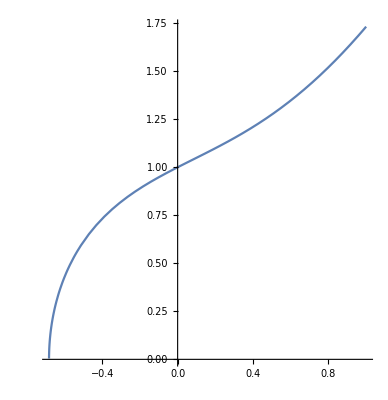

```mathematica
p1 = ParametricPlot[{t,Sqrt[t^3+t+1]},{t,-1,1}]
```

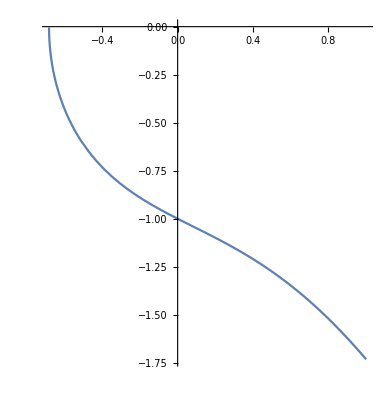

```mathematica
p2 = ParametricPlot[{t,-Sqrt[t^3+t+1]},{t,-1,1}]
```

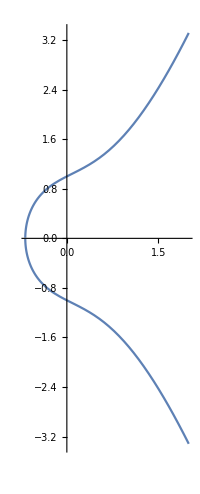

```mathematica
Show[p1,p2,PlotRange-> All]
```

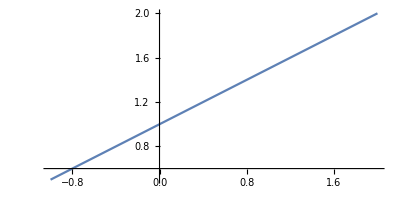

```mathematica
l1 = ParametricPlot[{t,(1/2)t+1},{t,-1,2}]
```

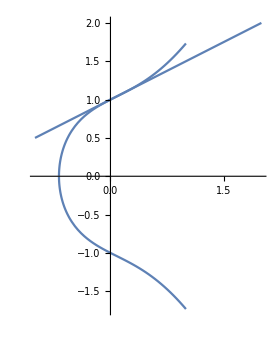

```mathematica
Show[p1,p2,l1,PlotRange-> All]
```

```mathematica
Solve[((1/2)x + 1)^2==x^3+x+1,x]
```

{{x→0},{x→0},{x→1/4}}

```mathematica
Solve[(-(17/2)x+1)^2 == x^3+x+1,x]
```

{{x→0},{x→1/4},{x→72}}

```mathematica
-(17/2)72+1
```

-611

```mathematica
610/72
```

305/36

```mathematica
Solve[((610/72)x+1)^2 == x^3+x+1,x]
```

{{x→-287/1296},{x→0},{x→72}}

```mathematica
(610/72)(-287/1296)+1
```

-40879/46656

```mathematica
64*((-3/16 - 1)(x-1/4)+2(-9/8) (y+9/8))/144//Expand
```

-143/144-(19 x)/36-y

```mathematica
Solve[(-143/144-(19 x)/36)^2 == x^3+x+1,x]
```

{{x→-287/1296},{x→1/4},{x→1/4}}

```mathematica
-143/144-(19 (-287/1296))/36
```

-40879/46656

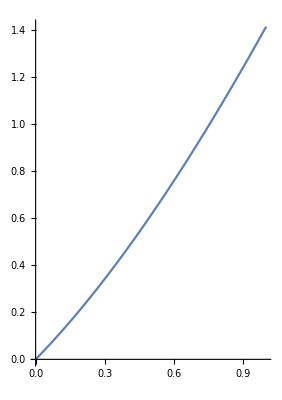

```mathematica
pp3=ParametricPlot[{t,Sqrt[t^3+t^2]},{t,0,1},PlotRange->All]
```

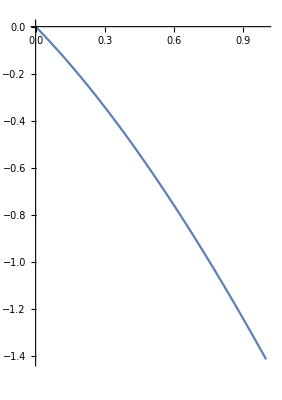

```mathematica
pp1=ParametricPlot[{t,-Sqrt[t^3+t^2]},{t,0,1},PlotRange->All]
```

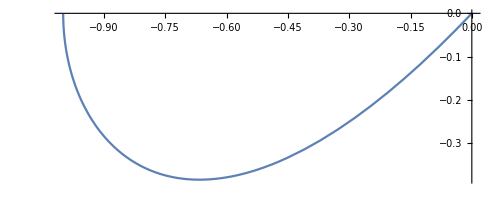

```mathematica
pp4 = ParametricPlot[{t,-Sqrt[t^3+t^2]},{t,-2,0},PlotRange->All]
```

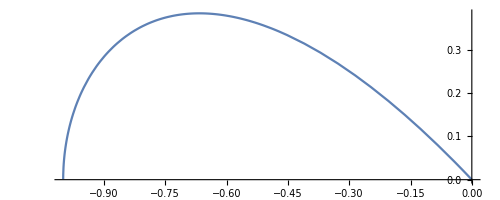

```mathematica
pp2 = ParametricPlot[{t,Sqrt[t^3+t^2]},{t,-2,0},PlotRange->All]
```

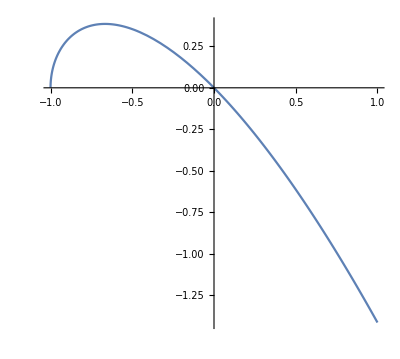

```mathematica
Show[pp1,pp2]
```

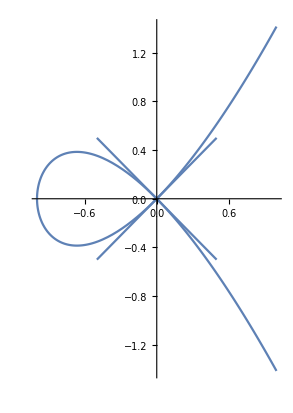

```mathematica
Show[pp1,pp2, pp3,pp4,ParametricPlot[{t,-t},{t,-1/2,1/2}],ParametricPlot[{t,t},{t,-1/2,1/2}]]
```

```mathematica
Limit[D[Sqrt[x^3+x^2],x],x-> 0]
```

1

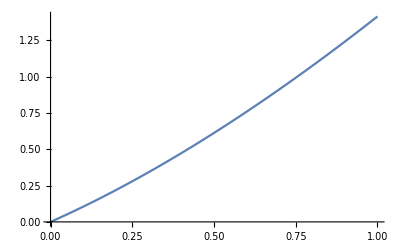

```mathematica
Plot[Sqrt[x^3+x^2],{x,0,1}]
```

```mathematica
Limit[Sqrt[h^3+h^2]/h,h-> 0,Direction->-1]
```

1

```mathematica
Limit[-Sqrt[h^3+h^2]/h,h-> 0,Direction->1]
```

1